# The N=2 characteristic polynomial

## Study the behavior of λ with q-ratio

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e, n==m}, {Sqrt[m+1]Sqrt[m+2](-v), n-m==2}, {Sqrt[m]Sqrt[m+1](-v), n-m==-2}}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
boson0[n_]:=Hmat02[n,1,q];
boson1[n_]:=Hmat13[n,1,q];
function[q_,n_]:=Table[Eigenvalues[boson0[n]][[id]],{id,1,Length[Eigenvalues[boson0[n]]]}];
```

```mathematica
function[q,2]
```

{1-√(1+2 √3 q^2),1+√(1+2 √3 q^2)}

```mathematica
proc[n_]:=Manipulate[Plot[function[q,n][[id]],{q,0,3}],{id,1,Length[Eigenvalues[boson0[n]]],1}];
```

```mathematica
proc[2]
```

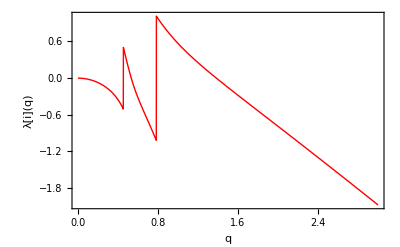

```mathematica
Plot[function[q,6][[6]],{q,0,3},Axes -> False, Frame -> True, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}]
```

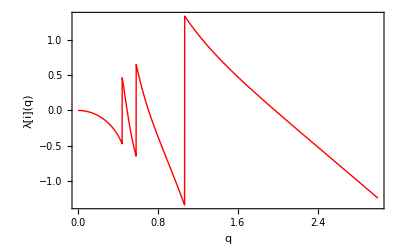

```mathematica
Plot[function[q,8][[8]],{q,0,3}, Axes -> False, Frame -> True, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}]
```

```mathematica
Evaluate[function[q,8][[8]]]
```

Root[-645120 √3 q^2+322560 √21 q^4+241920 √33 q^4+161280 √65 q^4+161280 √105 q^4+64512 √429 q^4-201600 √91 q^6-80640 √455 q^6-60480 √715 q^6-60480 √1155 q^6-32256 √3003 q^6-16128 √15015 q^6+75600 √1001 q^8+(-645120+513792 √3 q^2+322560 √7 q^2+241920 √11 q^2+322560 √15 q^2+161280 √35 q^2+64512 √143 q^2+53760 √195 q^2-403200 √13 q^4-162816 √21 q^4-138240 √33 q^4-103488 √65 q^4-222528 √105 q^4-120960 √165 q^4-67200 √273 q^4-60480 √385 q^4-39552 √429 q^4-32256 √1001 q^4-26880 √1365 q^4-52416 √2145 q^4-16128 √5005 q^4+246960 √91 q^6+151200 √143 q^6+28224 √455 q^6+25200 √715 q^6+9360 √1155 q^6+35568 √3003 q^6+19296 √15015 q^6) #1+(836352-163328 √3 q^2-324096 √7 q^2-259200 √11 q^2-176256 √15 q^2-141888 √35 q^2-71808 √143 q^2-61376 √195 q^2+157920 √13 q^4+27456 √21 q^4+27120 √33 q^4+23856 √65 q^4+49680 √105 q^4+38880 √165 q^4+48720 √273 q^4+39600 √385 q^4+8544 √429 q^4+26496 √1001 q^4+22848 √1365 q^4+30192 √2145 q^4+11232 √5005 q^4-22680 √91 q^6-25200 √143 q^6-2016 √455 q^6-2520 √715 q^6-360 √1155 q^6-13176 √3003 q^6-1296 √15015 q^6) #1^2+(-420224+26640 √3 q^2+108864 √7 q^2+96240 √11 q^2+37600 √15 q^2+39216 √35 q^2+28320 √143 q^2+25200 √195 q^2-20160 √13 q^4-1920 √21 q^4-2160 √33 q^4-2352 √65 q^4-3984 √105 q^4-3840 √165 q^4-8400 √273 q^4-5040 √385 q^4-768 √429 q^4-5760 √1001 q^4-5376 √1365 q^4-6384 √2145 q^4-1728 √5005 q^4) #1^3+(108304-2360 √3 q^2-15648 √7 q^2-15720 √11 q^2-3920 √15 q^2-4824 √35 q^2-5040 √143 q^2-4760 √195 q^2+840 √13 q^4+48 √21 q^4+60 √33 q^4+84 √65 q^4+108 √105 q^4+120 √165 q^4+420 √273 q^4+180 √385 q^4+24 √429 q^4+288 √1001 q^4+336 √1365 q^4+468 √2145 q^4+72 √5005 q^4) #1^4+(-15680+108 √3 q^2+1008 √7 q^2+1140 √11 q^2+200 √15 q^2+276 √35 q^2+408 √143 q^2+420 √195 q^2) #1^5+(1288-2 √3 q^2-24 √7 q^2-30 √11 q^2-4 √15 q^2-6 √35 q^2-12 √143 q^2-14 √195 q^2) #1^6-56 #1^7+#1^8&,8]